# Workhorse problem

```mathematica
Clear["Global`*"];
e = 1.60217*10^-19;
h = 6.62607004 * 10^-34;
m = 9.10938 * 10^-31;
ℏ = h/(2*Pi);
alpha = Sqrt[(2*m*e)/ℏ] * 10^-9;
```

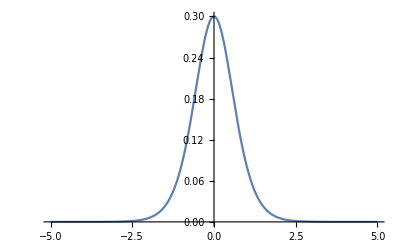

```mathematica
V[x_] = 0.3*(Sech[x])^3;
Plot[V[x],{x,-5,5}]
```

```mathematica
di = 10/15;
x = Table[i,{i,-5,5,di}]
```

{-5,-13/3,-11/3,-3,-7/3,-5/3,-1,-1/3,1/3,1,5/3,7/3,3,11/3,13/3,5}

```mathematica
k = alpha * Sqrt[en - V[x]]
```

{5.26109×10^-17 √(-7.34066×10^-7+en),5.26109×10^-17 √(-5.42199×10^-6+en),5.26109×10^-17 √(-0.0000400056+en),5.26109×10^-17 √(-0.000293992+en),5.26109×10^-17 √(-0.00212792+en),5.26109×10^-17 √(-0.0145569+en),5.26109×10^-17 √(-0.0816499+en),5.26109×10^-17 √(-0.254707+en),5.26109×10^-17 √(-0.254707+en),5.26109×10^-17 √(-0.0816499+en),5.26109×10^-17 √(-0.0145569+en),5.26109×10^-17 √(-0.00212792+en),5.26109×10^-17 √(-0.000293992+en),5.26109×10^-17 √(-0.0000400056+en),5.26109×10^-17 √(-5.42199×10^-6+en),5.26109×10^-17 √(-7.34066×10^-7+en)}

```mathematica
PI[kL_,kR_] = MatrixExp[1/2* Log[kL/kR] * (PauliMatrix[1] - IdentityMatrix[2])];
PP [kx_,l_] = MatrixExp[-I*kx*l*PauliMatrix[3]];
```

```mathematica
matrixelements = Table[PP[k[[index]], di].PI[k[[index]], k[[index+1]]], {index, 1, Length[x] - 1}];
M = IdentityMatrix[2];
For [i = 1, i≤ Length[matrixelements], i++, M = M.matrixelements[[i]]]
```

```mathematica
M = M.PP[k[[Length[x]]], di];
```

```mathematica
Plot[Abs[1/M[[1,1]]^2],{x,0.1,0.5}, PlotRange->All]
```

-Graphics-